## MCMC sampling code

Version 1.14.  Implementing parallelism within a single chain in the full parameter space.

## Random data from simulation

```mathematica
(* Import CSV file *)
alldata=Import[NotebookDirectory[]~~"Simulated_data_2021-07-27-14-59-41.csv"];
(* Extract data from CSV file.  z = redshifts; error = ±z;  nangledata = RA & Dec, converted to unit vector;  distmoddata = distance modulus *)
zdata=alldata[[All,1]];
errordata=alldata[[All,3]];
nangledata=alldata[[All,{4,5,6}]];
distmoddata=alldata[[All,2]];
```

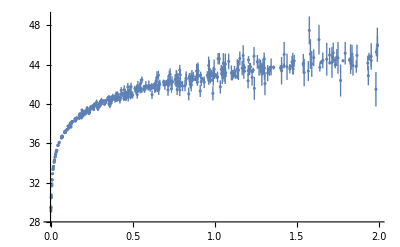

```mathematica
ListPlot[Transpose[{zdata,Thread[PlusMinus[distmoddata,errordata]]}]]
```

## Defining cosmological solution, constants, & constraints

```mathematica
(*Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];*)
zmax=2.; (*Trigger value to stop integration of background solution *)

(* Numerically solve ODEs for cosmic expansion. ParametricNDSolveValue does "setup" for ODEs but does not actually integrate them until called with a specific set of parameters.*)
ABvacmetric0=ParametricNDSolveValue[
{ⅇ^(-4 AA0[τ]+4 BB0[τ]) ΩB+ⅇ^(-2 AA0[τ]+2 BB0[τ]) Ωk+ⅇ^(-3 AA0[τ]) Ωm+ⅇ^(-4 AA0[τ]) Ωr+ΩΛ-AA0'[τ]^2+BB0'[τ]^2==0,ⅇ^(-4 AA0[τ]+4 BB0[τ]) ΩB+ⅇ^(-2 AA0[τ]+2 BB0[τ]) Ωk-1/3 ⅇ^(-4 AA0[τ]) Ωr+ΩΛ-AA0'[τ]^2+2 AA0'[τ] BB0'[τ]-BB0'[τ]^2-(2 AA0''[τ])/3+(2 BB0''[τ])/3==0,
WhenEvent[AA0'[τ]+2BB0'[τ]==0, Sow[True]; "StopIntegration"],(* Set flag to "True" & stop if we get to a contracting phase *)
WhenEvent[Exp[-(AA0[τ]+2BB0[τ])]-1>zmax+0.1&&Exp[-(AA0[τ]-BB0[τ])]-1>zmax+0.1,"StopIntegration"],
(* Stop if we get to z = zmax in all directions without entering a contracting phase *)
AA0[0]==BB0[0]==AA0'[0]-1==BB0'[0]-b0==0},{AA0,BB0},{τ,-∞,0},{ΩB,Ωk,Ωm,Ωr,ΩΛ,b0},Method->{"ParametricSensitivity"->None}]
c=299724.58 (* in km/s *)
paramconstraints=And[ΩB≥0,Ωm≥0,Ωr≥0] (* B-field density, matter density, and radiation denity must be positive*)
cExp=Compile[{{x,_Real}},If[x>-300.,Exp[x],0.](*,CompilationTarget->"C"*)]; (* Tried to make
```

ParametricFunction[<>]

299725.

ΩB≥0&&Ωm≥0&&Ωr≥0

## MCMC loop

```mathematica
(*LaunchKernels[];
ParallelEvaluate@Off[ParametricNDSolve::ndsz] ;(* Turn off "singularity" error message*)
ParallelEvaluate@Off[ParametricNDSolve::ndcf]; (* Turn off "repeated convergence failure" error message *)
ParallelEvaluate@Off[ParametricNDSolveValue::ntdvdae]; (* Turn off DAE warning *) 
ParallelEvaluate@Off[ParametricNDSolveValue::ndsz]; (* Turn off "singularity" warning *) *)

(*ParallelEvaluate@Off[General::munfl]; (* turn off "underflow" error *)*)
Off[ParametricNDSolve::ndsz] ;(* Turn off "singularity" error message*)
Off[ParametricNDSolve::ndcf]; (* Turn off "repeated convergence failure" error message *)
Off[ParametricNDSolveValue::ntdvdae]; (* Turn off DAE warning *) 
Off[ParametricNDSolveValue::ndsz]; (* Turn off "singularity" warning *) 

(* Generate random starting point in parameter space for Markov chain.  This is somewhat clunky since the parameter space isn't uniform but I want to pick a "nice" prior to avoid sampling bias.  It looks like I did some kind of rejection sampling that I will need to reconstruct.  Look at notes of 2021-07-30 et seq. *)  
sigma=1/10;
basedist=MultinormalDistribution[{0,3/10,0,7/10,0},sigma^2 IdentityMatrix[5]];
b0trunc=3;
hatdist=TruncatedDistribution[{{0,∞},{0,∞},{0,∞},{-∞,∞},{-b0trunc,b0trunc}},basedist];
max=√(5+4 b0trunc^2);
N[max]
randomstartpoint:=Module[{candpt,goodpt=False,Wk,b0,ctr},
While[!goodpt,
candpt=RandomVariate[hatdist];
b0=Last[candpt];
Wk=1-Total[Drop[candpt,-1]]-b0^2;
If[ RandomReal[{0,1}]<Exp[-Wk^2/(2 sigma^2)]√(5+4 b0^2)/max,goodpt=True];
];
Insert[candpt,Wk,2]
];
```

6.40312

```mathematica
totalpoints=10^4/4;
helperα=2; (* See notes of 2021-08-05.  IIRC this whole business is needed because Mathematica's NDSolve routine returns InterpolatingFunction objects that can dip below zero even if the "true" behavior of the function should never be negative.  This "helper alpha" was needed to get around this;  it parametrizes a transform between Subscript[ψ, o] and another function Subscript[υ, o].  *)
cθmin = 10^-6; (* Minimum abs. value of cos θ in helper-function calculation;  use extrapolation to get helper function values for smaller values of cos θ.  
At cos θ = 0, this cosmology has the property that z approaches a finite value as τ approaches the Big Bang.  This causes the code to stop integrating at that value of τ.  We avoid this by not actually integrating the redshift-luminosity relationship at cos θ = 0.  *)

(* Function below does one MCMC run, writing it to disk continuously. *)

mcdata[id_String]:=Module[{npoints=Round[totalpoints],counter,currentpt,paramspacedim,cosparamrules,helpersoln,distmod,χsq,currentchisq,candpt,chisqdata,ptdata,stepsize,acceptdatawindow,acceptdata,burnintime,fileid=id,savechunksize,paramsteps,candchisq,stepdump,initparams,initdirection,extrapflag,foo,ptstream,chisqstream,currentA,currentB,DcurrentA,DcurrentB,bbtime,contractflag},
counter=0;

(*{ΩB,Ωk,Ωm,Ωr,ΩΛ,b0,h,n0vec}*)
(*currentpt={0.1,0.079375,0.5,0.02,0.3,0.025,1,{0.40377356748395127,0.8197984306751251,0.4060756570688342}};*)
contractflag=True; (* Universes with "big bounces" are problematic, so we want to make sure the Universe is always expanding here.  If our parameters send us to a candidate state with a contracting phase, pick a different candidate state. *)
While[contractflag,
initparams=randomstartpoint;
initdirection=Normalize[RandomVariate[NormalDistribution[],3]];
currentpt=Join[initparams,{RandomReal[{0.5,1.5}]},{initdirection}];
(*currentpt={0.01,0.01,0.28,0.01,0.69,0,0.7,initdirection}; (* Our Universe, more or less *)*)
Print[currentpt];(* initial location *)

(*Calculation of initial chi-squared value *)
cosparamrules=Thread[{ΩB,Ωk,Ωm,Ωr,ΩΛ,b0}->currentpt[[1;;6]]];
{{currentA,currentB},contractflag}=ABvacmetric0@(Sequence@@Take[currentpt,6])//Reap; (* Evaluate cosmological solution for new candidate point in parameter space.  If it contracts at any point, a flag of True is "sown" when ParametricNDSolve is evaluated, and "reaped" here. *)
contractflag=Or@@Append[Flatten[contractflag],False]; 
(* See if any flags were sown.  If not, set contractflag to False, which ends the While loop.*)
];
DcurrentA=Derivative[1][currentA]; 
DcurrentB=Derivative[1][currentB]; (* Calculate derivatives of A & B functions.  Done once here to eliminate overhead in NDSolve call below. *)
bbtime=currentA["Domain"][[1,1]]; (* Time of the big bang for candidate parameters. *)

(* Integrate "helper functions" qo, te (emission time), and υo.  The latter is related to the ψo function from my notes. Note that this is invoked as a PDE that is zero-order in cos θ. This yields helper functions whose arguments are z & cos θ. *)
helpersoln=NDSolve[{
D[qo[z,cθ],z]==((DcurrentA[te[z,cθ]]+2DcurrentB[te[z,cθ]])Exp[-6 currentB[te[z,cθ]]] cθ^2+(DcurrentA[te[z,cθ]]-DcurrentB[te[z,cθ]])(1-cθ^2))^-1 UnitStep[te[z,cθ]-bbtime],
(* The above expression is called 𝒬 in my notes of 2021-07-07 *)
D[te[z,cθ],z]==-Exp[2currentA[te[z,cθ]]-2currentB[te[z,cθ]]] (1+z)D[qo[z,cθ],z]UnitStep[te[z,cθ]-bbtime],
D[υo[z,cθ],z]==(1-υo[z,cθ])^(helperα+1)Exp[-2currentA[te[z,cθ]]-4currentB[te[z,cθ]]] (1+z)^-2 D[qo[z,cθ],z]UnitStep[te[z,cθ]-bbtime],
qo[0,cθ]==te[0,cθ]==υo[0,cθ]==0},{qo,υo,te},{z,0,2},{cθ,cθmin,1},Method->{"Adams","PDEDiscretization"->{"MethodOfLines"}}];

(* Define predicted distance modulus function for current parameters, as function of z, sky position (nvec), cosmological parameters, and big bang time.  (Not sure why that last one is needed?) *)
distmod[z_,nvec_,paramlist_,bbtime_]:=Module[{cosparams=paramlist[[1;;6]],h=paramlist[[7]],n0vec=paramlist[[8]],cθ,teval,qoval,ψoval,υoval},
cosparamrules=Thread[{ΩB,Ωk,Ωm,Ωr,ΩΛ,b0}->cosparams];
cθ=nvec.n0vec; (* cos θ *)
{teval,qoval,υoval}={te[z,Abs[cθ]],qo[z,Abs[cθ]],υo[z,Abs[cθ]]}/.First[helpersoln]; (* extract te, qo, and υo *)
teval=Max[teval,bbtime]; (* If te ends up before the big bang, set it to BB time.  Still not sure why this is needed.  Could be issues with extrapolation in MM's solutions? *)
ψoval=Max[1/helperα(1/(1-υoval)^helperα-1),0]; (* Transform υo back into ψo *)
(*qoval=qo[cθ][z];
ψoval=ψo[cθ][z];*)
(* Calculated predicted distance modulus *)
-2.5 Log10[(Exp[2currentA[teval]+10currentB[teval]](h*10^-3/c)^2/((cθ^2+Exp[6currentB[teval]](1-cθ^2))^(5/2)qoval ψoval Re[Sinc[qoval √(-3 Ωk(1-cθ^2))]]))/.cosparamrules]
];
(* Function to calculate χ^2 for the given parameters *)
χsq[params_]:=∑_(i=1)^Length[zdata] (distmoddata[[i]]-distmod[zdata[[i]],nangledata[[i]],params,bbtime])^2/(errordata[[i]])^2;
currentchisq=χsq[currentpt]; (* initial chi-squared value *)

(* In this version of the code, the MCMC steps are written to file rather than being stored in memory *)
candpt=currentpt;
savechunksize=npoints/100;
ptstream=OpenWrite["Cosmological_MC_run_"~~fileid~~"_"~~ToString[$KernelID]~~".csv"];
chisqstream=OpenWrite["Cosmological_chisq_run_"~~fileid~~"_"~~ToString[$KernelID]~~".csv"];

(* Pick a step size.  This may need to be adjusted based on the properties of the distribution.  Optimal acceptance rate for many situations is about 0.234.  Code below is designed to monitor this rate in a "gauge" while running, though displaying the gauge incurs performance costs;  comment it out for better performance. *)
stepsize=10^-5;
acceptdatawindow=100;
acceptdata=ConstantArray[1,acceptdatawindow];  (* Initialize "acceptance tracker" data. 1 = accept, 0 = reject.  During main MCMC loop, this will be constantly overwritten to track how many of the last acceptdatawindow steps were accepted and which were rejected. *)
(*Dynamic[ProgressIndicator[counter,{0,npoints}]];
Print["Acceptance rate for last "~~ToString[acceptdatawindow]~~" steps:"];
Dynamic[BulletGauge[Total[acceptdata]/acceptdatawindow,0.234,{0,1}]];*)

(* Main loop *)

While[counter<npoints,
counter++;
extrapflag=False; (* Reset extrapolation flag, whatever that is *)
(*stepdump[[counter,1]]=currentchisq;
stepdump[[counter,2]]=currentpt;*)
(* Pick a random new candidate state & calculate its chi-squared value.  Start by generating random steps for all cosmological parameters except Subscript[Ω, k].*)
paramsteps=RandomReal[{-stepsize,stepsize},6];
(* Set steps in any "fixed" parameters to 0;  none currently. *)

(* Add steps to all parameters other than Subscript[Ω, k]. *)
candpt[[1]]=currentpt[[1]]+paramsteps[[1]];
candpt[[3;;7]]=currentpt[[3;;7]]+paramsteps[[2;;6]];

(* Calculate new value of Subscript[Ω, k] given steps in other parameters.  *)
candpt[[2]]=1-candpt[[1]]-candpt[[3]]-candpt[[4]]-candpt[[5]]-candpt[[6]]^2;

(* Make step for Subscript[n̂, 0], then renormalize.  This is a bit clunky but should work. *)
candpt[[8]]=Normalize[currentpt[[8]]+RandomVariate[NormalDistribution[0,stepsize],3]];

(*stepdump[[counter,4]]=candpt;*)

(* From here below the code is the same as my initialization code, above.  TBH it should probably be sequestered as its own routine and invoked at the appropriate moment. *)

cosparamrules=Thread[{ΩB,Ωk,Ωm,Ωr,ΩΛ,b0}->candpt[[1;;6]]];
{{currentA,currentB},contractflag}=ABvacmetric0@(Sequence@@Take[currentpt,6])//Reap;
contractflag=Or@@Append[Flatten[contractflag],False];
DcurrentA=Derivative[1][currentA];
DcurrentB=Derivative[1][currentB];
bbtime=currentA["Domain"][[1,1]];

If[(paramconstraints/.cosparamrules)&&!contractflag, (* Check if we're out of bounds before doing the hard work *)
helpersoln=
Check[foo=NDSolve[{
D[qo[z,cθ],z]==((DcurrentA[te[z,cθ]]+2DcurrentB[te[z,cθ]])Exp[-6 currentB[te[z,cθ]]] cθ^2+(DcurrentA[te[z,cθ]]-DcurrentB[te[z,cθ]])(1-cθ^2))^-1 UnitStep[te[z,cθ]-bbtime],
(* The above expression is called 𝒬 in my notes of 2021-07-07 *)
D[te[z,cθ],z]==-Exp[2currentA[te[z,cθ]]-2currentB[te[z,cθ]]] (1+z)D[qo[z,cθ],z]UnitStep[te[z,cθ]-bbtime],
D[υo[z,cθ],z]==(1-υo[z,cθ])^(helperα+1)Exp[-2currentA[te[z,cθ]]-4currentB[te[z,cθ]]] (1+z)^-2 D[qo[z,cθ],z]UnitStep[te[z,cθ]-bbtime],
qo[0,cθ]==te[0,cθ]==υo[0,cθ]==0},{qo,υo,te},{z,0,2},{cθ,cθmin,1},Method->{"Adams","PDEDiscretization"->{"MethodOfLines"}}],
extrapflag=True; foo,
InterpolatingFunction::dmval];
distmod[z_,nvec_,paramlist_,bbtime_]:=Module[{cosparams=paramlist[[1;;6]],h=paramlist[[7]],n0vec=paramlist[[8]],cθ,teval,qoval,ψoval,υoval},
cosparamrules=Thread[{ΩB,Ωk,Ωm,Ωr,ΩΛ,b0}->cosparams];
cθ=nvec.n0vec;
{teval,qoval,υoval}={te[z,Abs[cθ]],qo[z,Abs[cθ]],υo[z,Abs[cθ]]}/.First[helpersoln];
teval=Max[teval,bbtime];
ψoval=Max[1/helperα(1/(1-υoval)^helperα-1),0];
(*qoval=qo[cθ][z];
ψoval=ψo[cθ][z];*)
-2.5 Log10[(Exp[2currentA[teval]+10currentB[teval]](h*10^-3/c)^2/((cθ^2+Exp[6currentB[teval]](1-cθ^2))^(5/2)qoval ψoval Re[Sinc[qoval √(-3 Ωk(1-cθ^2))]]))/.cosparamrules]
];
χsq[params_]:=ParallelSum[(distmoddata[[i]]-distmod[zdata[[i]],nangledata[[i]],params,bbtime])^2/(errordata[[i]])^2,{i,Length[zdata]}];

(* Check for "extrapolation" error message;  set "extrapflag" true if so.  This occurs if one of the InterpolatingFunction objects is evaluated at an argument outside of its range of validity.  If the code is behaving right this shouldn't happen. *)
candchisq=Check[foo=χsq[candpt],extrapflag=True; foo,InterpolatingFunction::dmval]; 
If[extrapflag,Print["Extrapolation error encountered at step ",counter,". Candidate point: ",candpt]];
(*stepdump[[counter,3]]=candchisq;*)


(* Accept/reject the candidate state. Double bar "||" means "Or". *)
If[(candchisq≤currentchisq || RandomReal[{0,1}]<cExp[-(candchisq-currentchisq)])&&!extrapflag,
(* If passed, update current state and acceptance flag.  Use of "Mod" is designed to cycle through slots of acceptdata, so it always contains the last "acceptdatawindow" steps. *)
currentpt=candpt; currentchisq=candchisq; acceptdata[[Mod[counter,acceptdatawindow]+1]]=1, 
(* Otherwise, just update acceptance flag *)
acceptdata[[Mod[counter,acceptdatawindow]+1]]=0
] ;, (* end accept/reject check for in-bounds state *)
acceptdata[[Mod[counter,acceptdatawindow]+1]]=0 (* if candidate state is out of bounds *) 
] ; (* end out-of-bounds candidate check *) 

WriteString[chisqstream,TextString[currentchisq]~~"\n"];
WriteString[ptstream,StringDrop[StringDrop[TextString[currentpt],1],-1]~~"\n"];


(* Report out every so often *)
If[Mod[counter,savechunksize]==0,
(*Export["Cosmological_MC_run_"~~datestr~~"_All_"~~ToString[$KernelID]~~".csv",ptdata];
Export["Cosmological_MC_chisq_"~~datestr~~"_All_"~~ToString[$KernelID]~~".csv",chisqdata];*)
Print["Elapsed time: ",Now-starttime,". ",counter,"/",npoints," steps complete. Acceptance rate: ", N[Total[acceptdata]/acceptdatawindow], ". χ^2 = ",currentchisq];
(*SendMessage["SMS",StringJoin["Kernel ",TextString[$KernelID]," elapsed time: ",TextString[Now-starttime],". ",TextString[counter],"/",TextString[npoints]," steps complete. Acceptance rate: ", TextString[N[Total[acceptdata]/acceptdatawindow]], ". Chisq = ",TextString[currentchisq]]];*)
]; (* end report-out *)
]; (* end main loop *)
Close[ptstream];
Close[chisqstream];
(*{ptdata,chisqdata(*,stepdump*)}*)
] (* end module for MC run generation *)

$DateStringFormat={"Year","-","Month","-","Day","-","Hour","-","Minute","-","Second"};
datestr=DateString[];
Print["Start time: ",starttime=Now,". Memory in use: ",MemoryInUse[]];
mcdata[datestr];
Print["Elapsed time: ",Now-starttime,". Memory in use: ",MemoryInUse[]]
```

Start time: 2021-08-11-18-04-51GMT-4.. Memory in use: 673112256

{0.17035,-0.000339377,0.0723531,0.0349237,0.711304,-0.106811,0.675686,{-0.352347,0.325503,0.877439}}

Elapsed time: 13.9596 s. 25/2500 steps complete. Acceptance rate: 0.85. χ^2 = 2.32752×10^8

Elapsed time: 27.5648 s. 50/2500 steps complete. Acceptance rate: 0.72. χ^2 = 2.32659×10^8

Elapsed time: 41.0195 s. 75/2500 steps complete. Acceptance rate: 0.6. χ^2 = 2.32548×10^8

Elapsed time: 54.9285 s. 100/2500 steps complete. Acceptance rate: 0.48. χ^2 = 2.32423×10^8

Elapsed time: 1.14826 min. 125/2500 steps complete. Acceptance rate: 0.48. χ^2 = 2.32315×10^8

Elapsed time: 1.37148 min. 150/2500 steps complete. Acceptance rate: 0.48. χ^2 = 2.32215×10^8

Elapsed time: 1.60129 min. 175/2500 steps complete. Acceptance rate: 0.45. χ^2 = 2.32115×10^8

Elapsed time: 1.8343 min. 200/2500 steps complete. Acceptance rate: 0.47. χ^2 = 2.31964×10^8

Elapsed time: 2.05113 min. 225/2500 steps complete. Acceptance rate: 0.49. χ^2 = 2.31863×10^8

Elapsed time: 2.2684 min. 250/2500 steps complete. Acceptance rate: 0.5. χ^2 = 2.31742×10^8

Elapsed time: 2.48865 min. 275/2500 steps complete. Acceptance rate: 0.55. χ^2 = 2.31623×10^8

Elapsed time: 2.70093 min. 300/2500 steps complete. Acceptance rate: 0.46. χ^2 = 2.31603×10^8

Elapsed time: 2.9184 min. 325/2500 steps complete. Acceptance rate: 0.47. χ^2 = 2.31523×10^8

Elapsed time: 3.13392 min. 350/2500 steps complete. Acceptance rate: 0.44. χ^2 = 2.31434×10^8

Elapsed time: 3.35938 min. 375/2500 steps complete. Acceptance rate: 0.43. χ^2 = 2.31333×10^8

Elapsed time: 3.57826 min. 400/2500 steps complete. Acceptance rate: 0.47. χ^2 = 2.31226×10^8

Elapsed time: 3.80021 min. 425/2500 steps complete. Acceptance rate: 0.46. χ^2 = 2.31105×10^8

Elapsed time: 4.01547 min. 450/2500 steps complete. Acceptance rate: 0.48. χ^2 = 2.31004×10^8

Elapsed time: 4.23777 min. 475/2500 steps complete. Acceptance rate: 0.5. χ^2 = 2.3083×10^8

Elapsed time: 4.47666 min. 500/2500 steps complete. Acceptance rate: 0.52. χ^2 = 2.30734×10^8

Elapsed time: 4.71764 min. 525/2500 steps complete. Acceptance rate: 0.48. χ^2 = 2.30633×10^8

Elapsed time: 4.94298 min. 550/2500 steps complete. Acceptance rate: 0.4. χ^2 = 2.30591×10^8

Elapsed time: 5.18665 min. 575/2500 steps complete. Acceptance rate: 0.29. χ^2 = 2.30539×10^8

Elapsed time: 5.40895 min. 600/2500 steps complete. Acceptance rate: 0.3. χ^2 = 2.30404×10^8

Elapsed time: 5.6275 min. 625/2500 steps complete. Acceptance rate: 0.33. χ^2 = 2.30326×10^8

Elapsed time: 5.84677 min. 650/2500 steps complete. Acceptance rate: 0.39. χ^2 = 2.30254×10^8

Elapsed time: 6.06473 min. 675/2500 steps complete. Acceptance rate: 0.48. χ^2 = 2.30104×10^8

Elapsed time: 6.28977 min. 700/2500 steps complete. Acceptance rate: 0.5. χ^2 = 2.29937×10^8

Elapsed time: 6.51835 min. 725/2500 steps complete. Acceptance rate: 0.51. χ^2 = 2.29812×10^8

Elapsed time: 6.75941 min. 750/2500 steps complete. Acceptance rate: 0.49. χ^2 = 2.2972×10^8

Elapsed time: 7.07208 min. 775/2500 steps complete. Acceptance rate: 0.46. χ^2 = 2.2961×10^8

$Aborted

Elapsed time: 7.34684 min. Memory in use: 574627792

```mathematica
Speak["Mathematica is done."]
```

```mathematica
allptdata=Table[Import["Cosmological_MC_run_2021-07-14-17-30-24_"~~ToString[i]~~".csv","CSV"],{i,8}];
Dimensions[allptdata]
```

Import::nffil: File Cosmological_MC_run_2021-07-14-17-30-24_1.csv not found during Import.

Import::nffil: File Cosmological_MC_run_2021-07-14-17-30-24_2.csv not found during Import.

Import::nffil: File Cosmological_MC_run_2021-07-14-17-30-24_3.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

{8}

## Plotting the results

Code below this point is designed to generate data plots;  not as immediately important for the actual software.

```mathematica
(* Display time-series of data.  For more than 10^5 data points this takes some time. However, plotting the function may yield a better sense of the burn-in time. *)
ListPlot[Transpose[ptdata],ImageSize->Large]

(*Display sampled data and true distribution.  Note that plotting the latter may not be feasible for "real-life" distributions, which is kind of the point. *)
(*Row[{SmoothDensityHistogram[Drop[ptdata,burnintime],0.001,PlotRange->{{-5,5},{-5,5},Automatic},ImageSize->Medium,ColorFunction->ColorData[{"CherryTones","Reverse"}],PlotLabel->"Sampled data"],
DensityPlot[Exp[-chisq[{x,y}]],{x,-5,5},{y,-5,5},PlotRange->{Automatic,Automatic,All},ImageSize->Medium,ColorFunction->ColorData[{"CherryTones","Reverse"}],PlotLabel->"True distribution",PlotPoints->100]}]*)
```

ListPlot::lpn: Transpose[ptdata] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[ptdata],ImageSize→Large]

```mathematica
Dimensions[Flatten[Drop[Delete[allptdata,{{1},{2},{4}}],None,burnintime],1]]
```

{50000,10}

{{0.326814,0.254236,9.50398},{0.326814,0.254236,9.50398},{0.326814,0.254236,9.50398},{0.326814,0.254236,9.50398},{0.325531,0.254106,9.50516},{0.325531,0.254106,9.50516},{0.325531,0.254106,9.50516},49986,{0.41362,0.287139,9.72157},{0.414434,0.2863,9.71982},{0.414434,0.2863,9.71982},{0.414434,0.2863,9.71982},{0.415161,0.285409,9.71816},{0.415648,0.285088,9.71689},{0.415648,0.285088,9.71689}}
 |  |  |  |

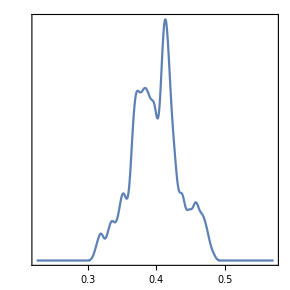
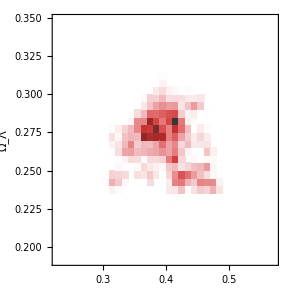
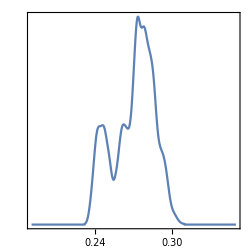
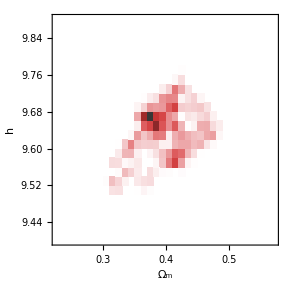
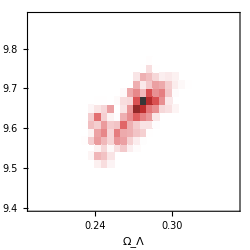
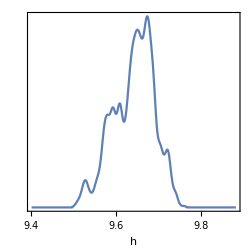
-Graphics- |  | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
burnintime=40000;
truncptdata=Flatten[Drop[Delete[allptdata,{{1},{2},{4}}],None,burnintime],1];
truncptdata=truncptdata[[All,{3,5,7}]]
paramnames={Subscript[Ω, m],Subscript[Ω, Λ],h};
numplots=Length[paramnames];
ranges={Mean[#]-5 StandardDeviation[#],Mean[#]+5 StandardDeviation[#]}&/@Transpose[truncptdata];
imsize=250; (* base size of images w/o labels *)
impadding=40; (* padding required for labels *)
(*ranges=Outer[Quantile,Transpose[truncptdata],{0.001,0.999},1] *)(* get ranges excluding 0.1% of outliers in either direction *)
staircaseplots=Grid[Table[
If[j<i, (* Scatter plot *)
DensityHistogram[Take[truncptdata[[All,{j,i}]]],
Frame->True,AspectRatio->1,Axes->None,
FrameLabel->{If[i==numplots,paramnames[[j]],None],If[j==1,paramnames[[i]],None]},
PlotRange->{ranges[[j]],ranges[[i]]},
FrameTicksStyle->{{If[j==1,Automatic,Directive[FontOpacity->0]],None},{If[i==numplots,Automatic,Directive[FontOpacity->0]],None}},
ImagePadding->{{If[j==1,impadding,1],1},{If[i==numplots,impadding,-10],1}},
ImageSize->{If[j==1,imsize+impadding,imsize],If[i==numplots,imsize+impadding,imsize]},
ColorFunction->ColorData[{"CherryTones","Reverse"}],
ColorFunctionScaling->True
(*FrameTicks->{{Automatic,None},{Chop[N[FindDivisions[ranges[[j]],8],{Infinity,2}],10^-2],None}}*)
],
If[j==i,(*Single-variable histogram *)
SmoothHistogram[Take[truncptdata[[All,i]]],(*Append[ranges[[i]],First[Differences[ranges[[i]]]]/(Ceiling[Log2[Length[truncptdata]]]+1)] (*bins chosen via Sturges' Rule*),*)
Frame->True,AspectRatio->1,Axes->None,
FrameLabel->{If[i==numplots,paramnames[[i]],None],None},
FrameTicks->{Automatic,None},
PlotRange->{ranges[[i]],Automatic},
FrameTicksStyle->{{Automatic,Automatic},{If[i==numplots,Automatic,Directive[FontOpacity->0]],None}},
ImagePadding->{{If[j==1,impadding,1],1},{If[i==numplots,impadding,-10],1}},
ImageSize->{If[j==1,imsize+impadding,imsize],If[i==numplots,imsize+impadding,imsize]}
],
Null]],
{i,1,numplots},{j,1,numplots}],Spacings->0]
```

```mathematica
Export["MCMC_cosmology_staircase_plot_2021-07-12.pdf",staircaseplots,ImageSize->1280]
```

MCMC_cosmology_staircase_plot_2021-07-12.pdf

```mathematica
datestr
```

2021-07-14-17-18-57